Discrete Probability

## Introduction

In this chapter you will learn how to use Mathematica to perform computations in discrete probability and how to use Mathematica's capabilities to explore concepts of discrete probability. We will continue to make use of the functions described in the previous chapter.

We will make use of simulations to help explore concepts in discrete probability. In this context, a simulation refers to a computer program that models a real physical system. For example, instead of flipping an actual coin one hundred times and recording whether each flip resulted in “heads” or “tails,” we could write a program that uses random numbers to generate a sequence of one hundred “heads” or “tails.”

Simulations are useful in discrete probability from two different perspectives. First, they can help analyze and/or confirm probabilities for systems that are difficult to compute deductively. For example, Computations and Explorations 7 from the text asks you to simulate the odd-person-out procedure in order to confirm your deductive calculations. Second, simulations can be very helpful as a way to better understand a problem and how to arrive at a solution. For example, in the Computer Projects 10 exercise, you are asked to build a simulation of the famous Monty Hall Three-Door problem. Building the simulation and analyzing the results can help improve your understanding of the reasons why the strategy described in the text is the best possible.

## 7.1 An Introduction to Discrete Probability

To find the probability of an event in a finite sample space, you calculate the number of times the event occurs and divide by the total number of possible outcomes (the size of the sample space).

As in Example 4, Section 7.1, we calculate the probability of winning a lottery, where we need to choose 6 numbers correctly out of 40 possible numbers. The total number of ways to choose 6 numbers is:

```mathematica
Binomial[40,6]
```

3838380

Since there is one winning combination, the probability is 1 divided by that value.

```mathematica
1/Binomial[40,6]
```

1/3838380

We can find a real number approximation by using the N function — evaluation as a floating point number. Given a single argument, N returns a numerical approximation of the value of the argument. With a positive integer as a second argument, you can control the number of digits of precision that are output.

```mathematica
N[1/Binomial[40,6]]
```

2.60527×10^-7

```mathematica
N[1/Binomial[40,6],20]
```

2.6052657631605000026×10^-7

We could also force a decimal approximation of the result by using 1.0 or simply 1., to show that we wish to work with decimals instead of the exact rational representation. For example, if we needed to choose from 50 numbers, the probability is

```mathematica
1.0/Binomial[50,6]
```

6.29299×10^-8

Continuing with this type of example, we define a function that computes the probability of winning a lottery where 6 numbers must be matched out of n possible numbers, provided that n is at least 6.

```mathematica
lottery[n_Integer]/;n≥6:=1.0/Binomial[n,6]
```

Then the probabilities above can be computed with the function.

```mathematica
{lottery[40],lottery[50]}
```

{2.60527×10^-7,6.29299×10^-8}

Now we can use the Table function to look at a list of probabilities for a range of values of n and graph these values with ListPlot to visualize how the number of possible values in the lottery affects the probability of choosing the correct values.

```mathematica
lotteryValues=Table[{n,lottery[n]},{n,40,50}]
```

{{40,2.60527×10^-7},{41,2.22401×10^-7},{42,1.90629×10^-7},{43,1.6403×10^-7},{44,1.41662×10^-7},{45,1.22774×10^-7},{46,1.0676×10^-7},{47,9.31309×10^-8},{48,8.14896×10^-8},{49,7.15112×10^-8},{50,6.29299×10^-8}}

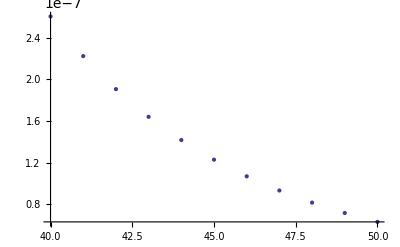

```mathematica
ListPlot[lotteryValues]
```

Refer to Section 2.3 of this manual for information on the use of ListPlot.

## 7.2 Probability Theory

We can use Mathematica to perform a variety of calculations of probabilities.

For example, Example 9 in section 7.2 asks us to calculate the probability that eight of the bits in a string of ten bits are 0s if the probability of a 0 bit is 0.9, the probability of a 1 bit is 0.1, and the bits are generated independently. To perform this calculation, we can input the formula directly:

```mathematica
Binomial[10,8]*0.9^8*0.1^2
```

0.19371

### Probability Distributions

We can think of this same question in terms of a random variable. Specifically, consider a random variable X that assigns to each string of ten bits the number of the bits that are 0s. Then the probability that eight of the ten bits were 0 is p(X=8).

In order to compute probabilities of events in terms of random variables, we must specify the distribution of the random variable.

#### Computing Probabilities from Discrete Distributions

Mathematica provides many different probability distributions, including several discrete distributions. To compute the probability of an event involving a random variable distributed according to a built-in distribution, you can use the Probability or NProbability functions. These functions are essentially identical, except NProbability applies numerical methods to approximate a numerical answer, while Probability uses symbolic methods. Using either function requires that we have a distribution, so we begin by introducing Mathematica’s implementation of the binomial distribution.

Theorem 2 in the textbook defines the binomial distribution, which is implemented in Mathematica as BinomialDistribution. The BinomialDistribution takes two parameters: the number of independent Bernoulli trials and the probability of a success. For the bit string example that began this section, there are 10 trials, and we interpret success to be a 0 bit, so the probability of success is 0.9. The binomial distribution with these parameters would be represented as shown below. Note that BinomialDistribution is not a function and evaluating the line below will do nothing.

BinomialDistribution[10,.9]

The Probability and NProbability functions expect two arguments. The first argument, written in terms of a symbol representing a random variable, is an expression describing an event. For example, to compute the probability p(X=8) in the bit-string example, the first argument would be X==8.

The second argument to the Probability and NProbability functions is used to indicate the distribution. This is done using the Distributed (\[Distributed]) function or operator. As a function, Distributed requires two arguments: the symbol representing the random variable and the representation of the distribution. To use the operator form, enter EscdistEsc to produce the \[Distributed] symbol. In this case, the name of the random variable goes on the left and the distribution on the right.

Putting these two pieces together, the expression below computes the probability of 8 successes for a binomial distribution with 10 trials and probability of success 0.9.

```mathematica
Probability[X==8,X\[Distributed]BinomialDistribution[10,.9]]
```

0.19371

Note that this is the same answer we found above using the formula.

Related to the binomial distribution is the probability distribution of a single Bernoulli trial. The BernoulliDistribution takes only one parameter, the probability of success. The following creates the random variable associated to a single trial with probability of success 0.9. The possible values of a Bernoulli random variable are 0 or 1, representing failure and success, respectively.

```mathematica
Probability[X==0,X\[Distributed]BernoulliDistribution[.9]]
```

0.1

Definition 1 of Section 7.1 defines the uniform distribution. Mathematica includes the distribution DiscreteUniformDistribution. Note that this is different from UniformDistribution, which is used for continuous random variables. The DiscreteUniformDistribution requires a single argument, a list containing the lower and upper bounds of the distribution. For example, the following computes the probability p(X^2≤4) for a random variable distributed uniformly on {-10,-9,…,9,10}.

```mathematica
Probability[X^2≤4,X\[Distributed]DiscreteUniformDistribution[{-10,10}]]
```

5/21

Definition 2 of Section 7.4 defines the geometric distribution. Mathematica uses a slightly different definition of geometric distribution than the textbook. In Mathematica, the value of a random variable distributed geometrically is the number of failures that occur before the first success, rather than the total number of trials until the first success. The GeometricDistribution in Mathematica requires one argument, the probability of success. The following computes the probability that if a coin with probability of heads 0.3 is flipped until it comes up heads, there will be at most 5 tails that appear.

```mathematica
Probability[X≤5,X\[Distributed]GeometricDistribution[.3]]
```

0.882351

Note that you can form more complicated events by including Boolean operators when building the event. For example, the probability that it requires at most 2 or at least 7 flips of a coin with probability of heads 0.3 before a heads comes up is:

```mathematica
Probability[X≤2||X≥7,X\[Distributed]GeometricDistribution[.3]]
```

0.739354

Mathematica also makes it easy to work with multiple distributions. For example, suppose you have two coins, one with probability of heads 0.3 and the other with probability of heads 0.25. The probability that flipping each coin once will result in at least one head can be computed as follows.

```mathematica
Probability[X==1||Y==1,{X\[Distributed]BernoulliDistribution[.3],Y\[Distributed]BernoulliDistribution[.25]}]
```

0.475

Note that the second argument is a list whose elements define the distributions for X and Y.

#### Graphing Probabilities

It is often useful to graph the probabilities associated to the values of a random variable. To do this, we will apply the DiscretePlot and PDF functions.

The DiscretePlot function is the discrete analog of Plot. Its first argument is an expression, the values of which are to be plotted, in terms of a variable. The second is a domain specification, which is of the same form as in a Table: {n,max}, {n,min,max}, {n,min,max,step}, or {n,list}, where n is the variable.

For example, the following plots the values of π(x), the function defined to be the number of primes less than or equal to the argument, for x∈{2,3,…,50}.

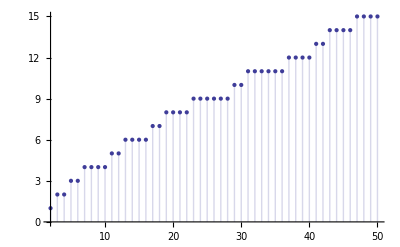

```mathematica
DiscretePlot[PrimePi[n],{n,2,50}]
```

By applying DiscretePlot with first argument an application of Probability, we can get a picture of a distribution.

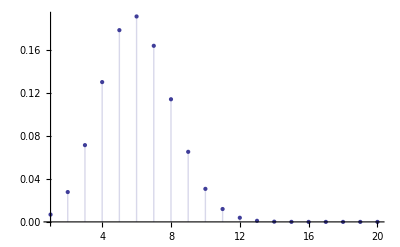

```mathematica
DiscretePlot[Probability[X==n,X\[Distributed]BinomialDistribution[20,.3]],{n,20}]
```

#### Conditional Probabilities

Mathematica allows you to calculate with conditional probabilities using the Conditioned (\[Conditioned]) operator. The operator symbol is entered by EsccondEsc. For example, consider a binomial random variable X with parameters 20 and 0.3. The probability that X is greater than 5 given that it is less than 10, that is p(X>5|X<10) can be compute as shown below.

```mathematica
Probability[X>5\[Conditioned]X<10,X\[Distributed]BinomialDistribution[20,.3]]
```

0.562653

#### Defining Distributions from Data

Mathematica provides the EmpiricalDistribution function to allow you to define, and thus compute with, discrete probability distributions from your own data. There are two ways to use the EmpiricalDistribution function.

If you have a list of values representing the results of experiments, you can pass this list of data to EmpiricalDistribution. For example, suppose you manually roll a die 20 times and obtain the following results.

```mathematica
dieRolls={3,2,1,1,5,2,3,6,5,1,2,5,6,4,4,3,1,3,1,1}
```

{3,2,1,1,5,2,3,6,5,1,2,5,6,4,4,3,1,3,1,1}

To use this as the basis for a distribution, simply give the list as the argument to EmpiricalDistribution. We’ll assign the distribution to a symbol.

```mathematica
dieDistribution=EmpiricalDistribution[dieRolls]
```

DataDistribution[«Empirical»,{20}]

The output is giving you a peek at the internal representation of the distribution. What’s important for us is that we can now use dieDistribution as a probability distribution in functions like Probability. For example, we can calculate the probability that the die shows a value of 4 or less.

```mathematica
Probability[X≤4,X\[Distributed]dieDistribution]
```

3/4

The second way you can use EmpiricalDistribution is to explicitly specify each data value and corresponding weights. As an example, consider the following problem. A die is weighted so that the probability of a 1 is 2/9, the probability of a 2 is 1/3, and the probability of the other values is 1/9 each. What is the probability that value is less than 3 when it is rolled?

To specify probabilities associated to specific values, you need to list the probabilities (or weights) and the values and join the two lists with a Rule (->). The following is the distribution of the die described above.

EmpiricalDistribution[{2/9,1/3,1/9,1/9,1/9,1/9}→{1,2,3,4,5,6}]

Mathematica interprets this as meaning that the data values in the right hand list are weighted as per the corresponding entry in the left hand list. That is, 1 has probability 2/9, 2 has probability 1/3, etc. Note that it is not necessary for the weights in the left hand list to be probabilities. Mathematica computes the probabilities of the data values by dividing the corresponding weight value by the sum of the weights. So the following will also produce the correct distribution for the die.

EmpiricalDistribution[{2,3,1,1,1,1}→{1,2,3,4,5,6}]

The following, therefore, computes the probability that the value is less than 3. Note that we use Range rather than type the integers 1 through 6.

```mathematica
Probability[X<3,X\[Distributed]EmpiricalDistribution[{2,3,1,1,1,1}->Range[6]]]
```

5/9

#### Combining Empirical Distributions

A more interesting question is to compute probabilities for the sum of the values on a weighted die. For example, consider two loaded dice. One is weighted so that the probability that a 1 appears is 2/7 and the probabilities of all other values is 1/7. The other is weighted to that the probability of a 4 appearing is 3/8 and the probabilities of all other values is 1/8. What is the probability that the sum is 7 when the two dice are rolled?

To answer this question, we first define two empirical distributions, just as done above. Here we assign the distributions to symbols.

```mathematica
weighted1=EmpiricalDistribution[{2,1,1,1,1,1}->Range[6]];
weighted2=EmpiricalDistribution[{1,1,1,3,1,1}->Range[6]];
```

The example above using two Bernoulli distributions suggests that the probability of the sum being 7 can be computed as below.

```mathematica
Probability[X+Y==7,{X\[Distributed]weighted1,Y\[Distributed]weighted2}]
```

9/56

#### Sampling

Given a particular distribution, you may wish to use it to conduct experiments or simulations. The process of generating pseudo-random numbers according to a given probability distribution is referred to as sampling. In Mathematica, the RandomVariate function is used to sample.

Recall that a random variable is a function that assigns a real number to each possible outcome in a sample space (Definition 6 in Section 7.2 of the textbook). A random variate is a real number obtained by applying the random variable to an outcome selected pseudo-randomly according to a specified probability distribution. In other words, where a random variable describes the relationship between an experiment’s sample space and real numbers, a random variate is a particular value obtained by performing the experiment.

Applying RandomVariate to a probability distribution produces a single random sample from that distribution. For example, the following expression simulates a binomial experiment with 10 trials and probability of success 0.4.

```mathematica
RandomVariate[BinomialDistribution[10,.4]]
```

4

Providing a positive integer as a second argument produces a list of that many values. For example, the following simulates a binomial process 1000 times.

```mathematica
binomialData=RandomVariate[BinomialDistribution[20,.3],1000];
```

We can use the Histogram function to draw a histogram of the data. You see that the data produced has approximately the same shape as was produced with PDF above. We use the PlotRange option, first described in Section 2.3, to ensure the graph shows all of the possible values, not just those actually obtained.

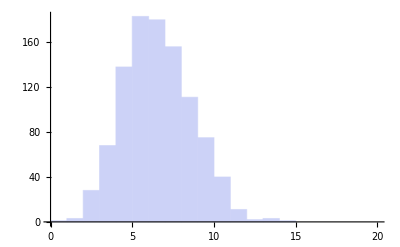

```mathematica
Histogram[binomialData,PlotRange->{{0,20},Full}]
```

### Monte Carlo Methods

We can also implement Monte Carlo algorithms using Mathematica. Miller's test for base b is described in the prelude to Exercise 44 of Section 4.4 of the textbook. In that description, it is mentioned that a composite integer n passes Miller's test for base b for fewer than n/4 bases less than n, and Exercise 44 asked you to show that primes pass Miller's test for all bases that they do not divide. In other words, Miller's test is a probabilistic primality test that fails less than one-fourth of the time. In this subsection we'll use Miller's test to create a Monte Carlo primality testing algorithm.

#### Miller’s Test

First we must implement Miller's test for base b. Recall the description preceding Exercise 44 in Section 4.4. Let n and b be positive integers. Assume s is a nonnegative integer and t is an odd positive integer such that n-1=2^s t. If b^t≡1 (mod n) or if there is a j with 0≤j≤s-1 such that b^(2^j t)≡-1 (mod n), then n is said to pass Miller's test for base b.

To implement Miller's test, we first must calculate s and t. Initialize s to 0 and set t equal to n-1. If t is even, we add 1 to s and divide t by 2. When t is no longer even, then s and t are the correct values.

Once s and t have been calculated, we check the congruence b^t≡1 (mod n). If that congruence is satisfied, then n passes Miller's test and we return True. Otherwise, we begin testing the congruences b^(2^j t)≡-1 (mod n). A For loop assigns j to each integer from 0 to s-1 and inside the For loop, the congruence is tested. If any congruence holds, the function returns True. (Recall from Section 4.1 of this manual that for exponentiation, PowerMod applied to an integer, an exponent, and a base is much more efficient than Mod. However, it returns the smallest positive integer congruent to its first argument modulo its second argument. That is, it will not return -1. Thus we test for congruence to -1 modulo n by comparing the result to n-1.) If the function completes without having returned True, then it returns False.

Note that we use Catch and Throw in order to ensure that the result becomes the output of the function.

```mathematica
miller[n_Integer,b_Integer]:=Module[{s=0,t=n-1,j},
While[Mod[t,2]==0,
t=t/2;
s++
];
Catch[
If[PowerMod[b,t,n]==1,Throw[True]];
For[j=0,j≤s-1,j++,
If[PowerMod[b,2^j*t,n]==n-1,Throw[True]]
];
Throw[False]
]
]
```

#### Monte Carlo Primality Test

Now we use Miller's test to implement a Monte Carlo primality testing algorithm, as described in Example 16 in section 7.2 of the text. The question the Monte Carlo algorithm is going to answer is “Is n composite?” for an integer n. For each iteration, the algorithm will select a random base b with 1<b<n and check to see if n passes Miller's test for base b. If Miller's test returns false, then we know that n is composite and the Monte Carlo algorithm will return “Composite.” If Miller's test returns true, then the iteration results in “unknown” and the next iteration is started. After 30 iterations, if Miller's test has only resulted in true, then the algorithm will return “Prime,” indicating that it is very likely that the number is prime. Since Miller's test falsely identifies a composite as prime less than one-fourth of the time, the probability that the Monte Carlo algorithm with 30 trials will incorrectly identify a composite number as prime is

```mathematica
(1/4)^30//N
```

8.67362×10^-19

Here is the Miller Monte Carlo test:

```mathematica
millerMC[n_Integer]:=Module[{b},
Catch[
Do[b=RandomInteger[{2,n-1}];
If[!miller[n,b],Throw["Composite"]]
,{30}];
Throw["Prime"]
]
]
```

Note the use of Do, with second argument {30}. This causes the body of the loop to be executed 30 times without assigning a loop variable, which in this case is not needed. The RandomInteger function applied to a list of two integers, with the first smaller than the second, produces a randomly selected integer in the range specified by the values.

Now we use millerMC to test an integer to see if it is prime. We can use Mathematica's Prime function to find the 40000th prime and then check that our algorithm confirms that it is prime.

```mathematica
Prime[40000]
```

479909

Now run the algorithm on this prime.

```mathematica
millerMC[479909]
```

Prime

## 7.3 Bayes’ Theorem

Section 7.3 focuses on applications of Bayes' Theorem, which asserts that for events E and F from a sample space S with p(E)≠0 and p(F)≠0, one has

p(F|E)=(p(E|F)p(F))/(p(E|F)p(F)+p(E|F̄)p(F̄))

The text describes how to use this theorem to create a Bayesian spam filter. We will use Mathematica to implement such a filter.

Recall the notation from the text. A message is received containing the word w. The event S will be the event that the message is spam and the event E is the event that the message contains the word w. If we assume that a message is as likely to be spam as not, so that p(S)=p(S̄)=1/2, then Bayes' Theorem tells us that the probability that the incoming message is spam given that it contains the word w is:

p(S|E)=(p(E|S))/(p(E|S)+p(E|S̄))

By estimating the conditional probabilities with empirical data, we can compute an estimate that the given message is spam.

Before building the spam filter, we will first need messages to serve as spam and non-spam. For the spam messages, we will use the sonnets of William Shakespeare, and for the non-spam messages, we will use sonnets written by Shakespeare's contemporaries, Michael Drayton, Bartholomew Griffin, and William Smith, published in the book Elizabethan Sonnet Cycles.

It may seem strange to consider Shakespeare's sonnets to be spam, but consider the goals and methods of a Bayesian spam filter. The goal of a spam filter is to filter out the “junk mail.” But in the case of the Bayesian filter described by the text, these filters work by comparing the specific words used by authors of spam in contrast to authors of non-spam messages. Think about email messages you receive from your classmates versus messages your professors may send you. Chances are good that you and your peers use more slang and generally less formal English when writing to each other than you and your professor use when communicating. This applies to kinds of message writers like peers versus professors, but it also can apply to individual message writers, like a mathematics professor versus a literature professor. A literature professor, for example, is not likely to use words like “Bayes' Theorem” in an email to you. A Bayesian spam filter can pick up on these differences in word choice and filter messages based on the assumption that different authors generally use different words. We will see, by comparing Shakespeare with other Elizabethan sonnet writers, that a Bayesian filter can even distinguish one author from others writing at the same time, for the same audience, and in a similar form.

#### Obtaining Data

On the website for this manual, you will find these three files: “ShakespeareData.txt”, “ElizabethanData.txt” and “testMessages.txt”. The first two contain the sonnets of Shakespeare and the other authors, respectively. Five of Shakespeare's poems and five of the other authors' poems were randomly selected and moved to the “testMessages.txt” file. We will use our filter on the poems in this file to determine which of them were written by Shakespeare and which were not.

Begin by downloading the three files and storing them in the same directory as this Mathematica Notebook. Then load the three files and store the text in variables using the Import function, as shown below.

```mathematica
shakespeare=Import["ShakespeareData.txt",Path->NotebookDirectory[]];
```

```mathematica
elizabethan=Import["ElizabethanData.txt",Path->NotebookDirectory[]];
```

```mathematica
test=Import["testMessages.txt",Path->NotebookDirectory[]];
```

The Import function is able to load a variety of file types for processing with Mathematica, including images, sounds, video, spreadsheets, and many others. In this case, Import loads the files, which consist exclusively of text, and stores them as a string. The Path option is used to tell Mathematica what directory on your computer contains the file. The NotebookDirectory function, which takes no arguments, returns the directory in which the current notebook is stored. So provided that you downloaded the three data files to the same directory as the one holding this notebook, the above should load the three files. If not, you may need to move the files to the correct location or specify the directory manually.

If you inspect these files in a text editor, you will see that the sonnets are separated by three ampersands (“&&&”). The three expressions above store each of the files as a single string. It would be more useful to store them as lists of strings, with each sonnet being one element of a list. To separate the files into lists, we use StringSplit.

```mathematica
sPoems=StringSplit[shakespeare,"&&&"];
```

```mathematica
ePoems=StringSplit[elizabethan,"&&&"];
```

```mathematica
testPoems=StringSplit[test,"&&&"];
```

The StringSplit function splits the string in the first argument based on the pattern given in the second argument. In this case, the pattern is the string “&&&” so the StringSplit command uses that pattern as a delimiter in the shakespeare, elizabethan, and test strings to separate them into lists. Now that the “messages” are prepared, we begin building the filter.

#### Estimating the Probabilities

The spam filter relies on two computations: first, the probability that a message contains a word given that it is spam, and second, the probability that a message contains the word given that it is not spam. That is, we will need empirical estimates for p(E|S) and p(E|S̄).

Following the notation of the textbook, for a word w, let p(w) be the estimate of p(E|S), the probability that a message contains w given that it is spam. So p(w) is the number of spam messages containing the word w divided by the number of spam messages. Likewise, let q(w) be the estimate for p(E|S̄), the probability that a message contains w given that it is not spam. This is computed as the number of non-spam messages containing w divided by the number of non-spam messages.

Counting the number of messages (i.e., poems) in each list can be done with Length.

```mathematica
Length[sPoems]
```

149

(This is five less than the 154 sonnets that Shakespeare published, because five of them were moved to the “testMessages.txt” file as “unknown” messages.)

To count the number of messages that contain a particular word, we'll make use of StringFreeQ. This function accepts as arguments a string and a string pattern and returns true if the pattern does not appear in the string and false if it does. As a first example, the following determines that the substring “bc” does appear in the string “abcdefg”.

```mathematica
StringFreeQ["abcdefg","bc"]
```

False

However, this is not quite sufficient to check for the presence of words. To see why, consider the fifth sonnet.

```mathematica
sPoems[[5]]
```

Those hours, that with gentle work did frame
The lovely gaze where every eye doth dwell,
Will play the tyrants to the very same
And that unfair which fairly doth excel;
For never-resting time leads summer on
To hideous winter, and confounds him there;
Sap checked with frost, and lusty leaves quite gone,
Beauty o'er-snowed and bareness every where:
Then were not summer's distillation left,
A liquid prisoner pent in walls of glass,
Beauty's effect with beauty were bereft,
Nor it, nor no remembrance what it was:
  But flowers distill'd, though they with winter meet,
  Leese but their show; their substance still lives sweet.

If you look carefully, you will see that this poem does not contain the English word “so”. However, StringFreeQ returns false, indicating the presence of “so”:

```mathematica
StringFreeQ[sPoems[[5]],"so"]
```

False

The reason for this is the presence of the letters “so” within the word “prisoner” in line 10. To avoid this, we need to indicate that the word being sought must be surrounded by characters that do not appear in words. To do this, we’ll use the pattern

Except[WordCharacter|"'"]~~"so"~~Except[WordCharacter|"'"]

At the center of the pattern above is the word being sought, “so”. On either side of “so” we use two tildes, which is the StringExpression (~~) operator. You can think of ~~ as a concatenation operator for string patterns. On the far sides of the pattern is an application of Except. Within a string pattern, Except indicates that the pattern will match anything other than what is described by its argument. Recall that our goal is to insist that the word “so” be surrounded by non-word characters. Putting all the characters allowed to be in words inside of Except will accomplish this. Mathematica has a built-in symbol, WordCharacter, which stands for all letter and digit characters. We also recognize the frequent use of apostrophes in Elizabethan writing, and so we want to allow apostrophes within words. To do this, we use the Alternatives (|) operator and the string containing an apostrophe within the Except. For string patterns, Alternatives (|) is the equivalent of a logical “or.” Including the apostrophe will allow this pattern to recognize the string “distill’d” as a complete word instead of interpreting that string as two words, “distill” and “d”.

Using the pattern above in StringFreeQ correctly determines that the word “so” does not appear in poem 5.

```mathematica
StringFreeQ[sPoems[[5]],Except[WordCharacter|"'"]~~"so"~~Except[WordCharacter|"'"]]
```

True

Finally, Mathematica is, by default, case sensitive. This is a problem because StringFreeQ will not recognize the presence of a word if asked about the same word with a different capitalization. For example, the following indicates that “those”, the first word of poem five, is absent from it.

```mathematica
StringFreeQ[sPoems[[5]],Except[WordCharacter|"'"]~~"those"~~Except[WordCharacter|"'"]]
```

True

To correct this, we use set the option IgnoreCase to True.

```mathematica
StringFreeQ[sPoems[[5]],Except[WordCharacter|"'"]~~"those"~~Except[WordCharacter|"'"],IgnoreCase->True]
```

False

We use what we’ve done above as a model to create a function that takes a poem and a word as arguments and returns True if the word appears in the poem and False if not.

```mathematica
wordQ[poem_String,word_String]:=!StringFreeQ[poem,Except[WordCharacter|"'"]~~word~~Except[WordCharacter|"'"],IgnoreCase->True]
```

This function tells us that poem 5 does not include the word “so” but does contain the word “those”.

```mathematica
wordQ[sPoems[[5]],"so"]
```

False

```mathematica
wordQ[sPoems[[5]],"those"]
```

True

Now that we have a function that determines whether or not a particular word appears in a poem, we can determine the number of poems in a list that contain the word. We can do this simply by looping over all the poems in a list and incrementing a counter for those containing the word. Below, the Do loop with second argument {p,L} iterates over each poem p in the list of poems L.

```mathematica
countMessages[word_String,L:{__String}]:=Module[{count=0,p},
Do[If[wordQ[p,word],count++],
{p,L}];
count
]
```

For instance, we can see how many times Shakespeare uses the word “fairest” in a sonnet.

```mathematica
countMessages["fairest",sPoems]
```

4

So the empirical probability that a sonnet contains the word “fairest” given that it was written by Shakespeare is:

```mathematica
countMessages["fairest",sPoems]/Length[sPoems]
```

4/149

And the probability that a sonnet contains the word “fairest” given that it was written by one of our other authors is:

```mathematica
countMessages["fairest",ePoems]/Length[ePoems]
```

10/173

Applying Bayes' Theorem, we can compute the probability that a sonnet was written by Shakespeare given that it contains the word “fairest”:

```mathematica
(4/149)/(4/149+10/173)//N
```

0.31714

The above computation illustrates how to write a function to compute the probability that a sonnet is spam (i.e., was written by Shakespeare) given that it contains a specific word:

```mathematica
pShakespeareGivenWord[word_String]:=Module[{sCount,eCount,pWordGivenS,pWordGivenNotS},
sCount=Length[sPoems];
eCount=Length[ePoems];
pWordGivenS=countMessages[word,sPoems]/sCount;
pWordGivenNotS=countMessages[word,ePoems]/eCount;
N[pWordGivenS/(pWordGivenS+pWordGivenNotS)]
]
```

For example, the probability that a sonnet is Shakespearean given that it contains the word “beauty” is:

```mathematica
pShakespeareGivenWord["beauty"]
```

0.54468

#### Using Multiple Words

We can improve the filter by using multiple words, rather than just one. Using the notation of the text, let p(w_i) and q(w_i) be the probabilities that a message contains word w_i given that it is spam and that it is not spam, respectively. Then the probability that a message is spam given that it contains all of the words w_1,w_2,…,w_k is:

r(w_1,w_2,…,w_k)=(∏_(i=1)^k p(w_i))/(∏_(i=1)^k p(w_i)+∏_(i=1)^k q(w_i))

The Product function is useful here. Recall that we compute ∏_(i∈S)^ i^2 for S={1,3,5,7,9} with

```mathematica
Product[i^2,{i,{1,3,5,7,9}}]
```

893025

For instance, to compute the probability that a message contains the words “from”, “fairest”, and “creatures”:

```mathematica
S={"from","fairest","creatures"};
Product[countMessages[w,sPoems]/Length[sPoems],{w,S}]
```

456/3307949

We can modify our pShakespeareGivenWord function to work on lists of words instead of single words by putting the probability computations inside of Product commands. It's also a good idea to protect against division by zero errors, so we'll put the division inside of an if statement. This is needed in case one or more of the selected words appears in none of the sonnets by either author. In this case, we default to a probability of 0.5.

```mathematica
pShakespeareGivenList[L_List]:=Module[{sCount,eCount,pGivenS,pGivenNotS},
sCount=Length[sPoems];
eCount=Length[ePoems];
pGivenS=Product[countMessages[w,sPoems]/sCount,{w,L}];
pGivenNotS=Product[countMessages[w,ePoems]/eCount,{w,L}];
If[pGivenS+pGivenNotS≠0,
N[pGivenS/(pGivenS+pGivenNotS)],
0.5
]
]
```

So the probability that a sonnet is by Shakespeare given that it contains the words “from”, “fairest”, and “creatures” is:

```mathematica
pShakespeareGivenList[{"from","fairest","creatures"}]
```

0.55169

#### Selecting Test Words Randomly

Finally, we can use the RandomSample function to randomly select words from a test message, and then use those randomly selected words to compute the probability that the message was written by Shakespeare. Here's the first test message in “testMessages.txt”:

```mathematica
testPoems[[1]]
```

When to the sessions of sweet silent thought
I summon up remembrance of things past,
I sigh the lack of many a thing I sought,
And with old woes new wail my dear time's waste:
Then can I drown an eye, unused to flow,
For precious friends hid in death's dateless night,
And weep afresh love's long since cancell'd woe,
And moan the expense of many a vanish'd sight:
Then can I grieve at grievances foregone,
And heavily from woe to woe tell o'er
The sad account of fore-bemoaned moan,
Which I new pay as if not paid before.
  But if the while I think on thee, dear friend,
  All losses are restor'd and sorrows end.

First we must separate the poem into individual words. We do this using StringSplit, which we used to split the data files into individual poems. Instead of splitting on a special delimiter, such as “&&&”, we’ll use the pattern Except[WordCharacter|"'"]] that we determined earlier expressed non-word characters. In order to avoid having individual spaces in the list, which can happen when spaces and punctuation appear together with ends of lines, we will follow the pattern with the Repeated (..) operator. This way, two spaces, or a period followed by a space, will count as a single word delimiter.

```mathematica
exampleTestWords=StringSplit[testPoems[[1]],Except[WordCharacter|"'"]..]
```

{When,to,the,sessions,of,sweet,silent,thought,I,summon,up,remembrance,of,things,past,I,sigh,the,lack,of,many,a,thing,I,sought,And,with,old,woes,new,wail,my,dear,time's,waste,Then,can,I,drown,an,eye,unused,to,flow,For,precious,friends,hid,in,death's,dateless,night,And,weep,afresh,love's,long,since,cancell'd,woe,And,moan,the,expense,of,many,a,vanish'd,sight,Then,can,I,grieve,at,grievances,foregone,And,heavily,from,woe,to,woe,tell,o'er,The,sad,account,of,fore,bemoaned,moan,Which,I,new,pay,as,if,not,paid,before,But,if,the,while,I,think,on,thee,dear,friend,All,losses,are,restor'd,and,sorrows,end}

We apply DeleteDuplicates to remove repeated words.

```mathematica
exampleTestWords=DeleteDuplicates[exampleTestWords]
```

{When,to,the,sessions,of,sweet,silent,thought,I,summon,up,remembrance,things,past,sigh,lack,many,a,thing,sought,And,with,old,woes,new,wail,my,dear,time's,waste,Then,can,drown,an,eye,unused,flow,For,precious,friends,hid,in,death's,dateless,night,weep,afresh,love's,long,since,cancell'd,woe,moan,expense,vanish'd,sight,grieve,at,grievances,foregone,heavily,from,tell,o'er,The,sad,account,fore,bemoaned,Which,pay,as,if,not,paid,before,But,while,think,on,thee,friend,All,losses,are,restor'd,and,sorrows,end}

Then randomly select four of those words.

```mathematica
exampleTestList=RandomSample[exampleTestWords,4]
```

{before,afresh,precious,many}

And then use our function to find the probability that a message with these four words was written by Shakespeare:

```mathematica
pShakespeareGivenList[exampleTestList]
```

0.5

Putting this all together:

```mathematica
pShakespeare[testMessage_String,testSize_Integer]:=Module[{testWordList},
testWordList=RandomSample[DeleteDuplicates[StringSplit[testMessage,Except[WordCharacter|"'"]..]],testSize];
pShakespeareGivenList[testWordList]
]
```

As an example, we'll run the filter on the second test message with a test size of 3.

```mathematica
pShakespeare[testPoems[[2]],3]
```

0.

## 7.4 Expected Value and Variance

In Section 7.2 of this manual, we introduced Mathematica's functions for using random variables, random variates, and probability distributions. In this section we will explore Mathematica's abilities more closely and use probability distributions to explore the concepts of expected value and variance.

As mentioned earlier, Mathematica provides the distribution GeometricDistribution, which takes one parameter, the probability of a “success.”

We can use the Probability function to compute the probabilities of events. For example, the probability p(X=5) is computed by the following.

```mathematica
Probability[X==5,X\[Distributed]GeometricDistribution[1/4]]
```

243/4096

Note that the Mathematica's definition of a geometric random variable differs slightly from the textbook's. The textbook defines the value of the geometric random variable, in terms of coin flips, to be the number of flips it takes to get a tails, where the parameter is the probability of tails. Mathematica's definition is that the value of the random variable is the number of heads that appear before tails comes up. So the probability p(X=k) is

```mathematica
Probability[X==k,X\[Distributed]GeometricDistribution[1/4]]
```

Piecewise[{{3^k 4^(-1-k), k≥0}, {0, True}}]

Contrast this with the formula given in the text.

Mathematica can also calculate the expected value, variance, and standard deviation of distributions. The Mean, Variance, and StandardDeviation functions all accept a distribution as the sole argument and return the statistic.

```mathematica
Mean[GeometricDistribution[1/4]]
```

3

```mathematica
Variance[GeometricDistribution[1/4]]
```

12

These functions can also compute symbolically:

```mathematica
StandardDeviation[GeometricDistribution[k]]
```

(√(1-k))/k

All three functions can also accept a list holding data. For example, to compute the mean of {1,3,4,7,11}:

```mathematica
Mean[{1,3,4,7,11}]
```

26/5

Alternately, you can use the Expectation function. Expectation is more flexible in that it allows you to form an expression using random variables as a first argument and specify the distributions of the random variables as the second argument. The syntax is similar to that of Probability, except the first argument is an expression, not an event.

For example, the following will find the expected value of the geometric distribution with parameter 1/4.

```mathematica
Expectation[X,X\[Distributed]GeometricDistribution[1/4]]
```

3

Expectation allows us to find the expected value of more complicated expressions, such as E(X^2).

```mathematica
Expectation[X^2,X\[Distributed]GeometricDistribution[1/4]]
```

21

Recalling that the variance of a random variable is E((X-E(X))^2), we can use Expectation to compute variance as well.

```mathematica
mean=Expectation[X,X\[Distributed]GeometricDistribution[1/4]]
```

3

```mathematica
Expectation[(X-mean)^2,X\[Distributed]GeometricDistribution[1/4]]
```

12

You can also mix distributions, as shown below.

```mathematica
distribution1=GeometricDistribution[1/4];
```

```mathematica
distribution2=BinomialDistribution[20,.3];
```

```mathematica
mean2=Expectation[X+2*Y,{X\[Distributed]distribution1,Y\[Distributed]distribution2}]
```

15.

```mathematica
Expectation[((X+2*Y)-mean2)^2,{X\[Distributed]distribution1,Y\[Distributed]distribution2}]
```

28.8

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 7

Given a positive integer m, simulate the collection of cards that come with the purchase of products to find the number of products that must be purchased to obtain a full set of m different collector cards. (See Supplementary Exercise 33.)

Solution: We will define a function called cardSimulate that will simulate the process of choosing random collectible cards until all the possible cards have been obtained. This function needs to do three things: (1) keep track of which cards have been obtained; (2) keep selecting random cards until the complete set is obtained; and (3) keep track of how many cards have been purchased.

Think of the cards as numbered 1 through m. To keep track of which cards have been obtained and which have not, we'll use a list that we'll call currCollection, for current collection. The entries in this list will be 0s and 1s, with a 0 representing the fact that the card corresponding to that position is not owned and 1 that it is. To initialize currCollection, we use the ConstantArray function. For example, to produce a list of ten 0s, you would enter the following.

```mathematica
ConstantArray[0,10]
```

{0,0,0,0,0,0,0,0,0,0}

Second, random selection of integers can be accomplished with the RandomInteger function. When given an argument of the form {min,max}, RandomInteger returns an integer selected from that range. Our cards are numbered 1 through m, so we will use the range specification {1,m}.

```mathematica
RandomInteger[{1,10}]
```

4

Our function will generate a random card and set the entry in currCollection at that card's position equal to 1. This needs to keep happening until all the cards are owned. So we need to know when all of the entries of the list are 1s. We can do this by adding up the entries in the list. Since the entries are always 0 or 1, when the list is all 1s, the sum will be equal to m and that's the only way the sum can be m. To add the entries in the list, we can use the Total function as follows.

```mathematica
Total[{1,0,0,1,1,1}]
```

4

Third, we keep track of how many cards have been purchased with a counter that we increment each time a random card is generated.

Putting all of these pieces together, here is the function:

```mathematica
cardSimulate[m_Integer]:=Module[{currCollection,count,tempCard},
currCollection=ConstantArray[0,m];
count=0;
While[Total[currCollection]≠m,
tempCard=RandomInteger[{1,m}];
count++;
currCollection[[tempCard]]=1
];
count
]
```

Let's run the simulation 10000 times for m=5 and draw a graph of the resulting data:

```mathematica
simulations=Table[cardSimulate[5],{10000}];
```

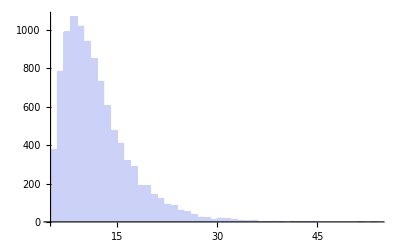

```mathematica
Histogram[simulations]
```

### Computer Projects 9

Given a positive integer n, find the probability of selecting the six integers from the set {1,2,…,n} that were mechanically selected in a lottery.

Solution: We will follow example 4 from Section 7.1 of the text. The total number of ways of choosing 6 numbers from n numbers is C(n,6), which is found with the function Binomial. This gives us the total number of possibilities, only one of which will win. The following defines this function and applies it to the situation in which n=49.

```mathematica
lottery[n_Integer]:=1./Binomial[n,6]
```

```mathematica
lottery[49]
```

7.15112×10^-8

If the rules of the lottery change, so that the number of numbers chosen is something other than 6, then we must modify the function above. We can easily modify our program to allow us to specify how many numbers we want to choose, by adding another parameter.

```mathematica
lottery2[n_Integer,k_Integer]:=1./Binomial[n,k]
```

```mathematica
lottery2[49,6]
```

7.15112×10^-8

```mathematica
lottery2[30,3]
```

0.000246305

### Computations and Explorations 3

Estimate the probability that two integers selected at random are relatively prime by testing a large number of randomly selected pairs of integers. Look up the theorem that gives this probability and compare your results with the correct probability.

Solution: To solve this problem, three things must be done:

Devise a method for generating pairs of random integers.

Produce a large number of these pairs, test whether they are relatively prime, and note the probability estimate based on this sample.

Look up the theorem mentioned in the question.

Naturally, we'll leave part 3 entirely to the reader.

The Mathematica function RandomInteger can be used to generate a the random integers. The optional second argument can be used to specify a number of integers to generate. For example, the following generates 10 random integers between 0 and 100.

```mathematica
RandomInteger[100,10]
```

{61,61,49,60,42,20,77,2,83,81}

The second argument can also specify that a nested list should be generated. For example, to generate ten pairs of integers, you use {10,2} as the second argument.

```mathematica
RandomInteger[100,{10,2}]
```

{{70,45},{5,76},{23,51},{42,71},{99,99},{19,100},{45,8},{23,68},{29,8},{7,82}}

Having generated such a list we can test whether the pairs of its members are relatively prime using the Mathematica function CoprimeQ. We can evaluate CoprimeQ on each pair by using Apply (@@) at level 1. Ordinarily, Apply replaces the head of an expression with the function being applied. In this case, we want to apply the function CoprimeQ not to the entire expression, but “one level down” at each subexpression. For this, we can give the level specification {1} as a third argument in the Apply function.

```mathematica
Apply[CoprimeQ,RandomInteger[100,{10,2}],{1}]
```

{False,True,False,True,False,False,False,True,False,False}

Alternately, you can use the @@@ operator.

```mathematica
CoprimeQ@@@RandomInteger[100,{10,2}]
```

{False,True,True,True,False,False,False,True,True,False}

Now we just need to count the number that are relatively prime. For this, we use the Count function with second argument True to count the number of times that True appears in the list.

```mathematica
Count[CoprimeQ@@@RandomInteger[100,{10,2}],True]
```

7

Increase the maximum integer and the number of pairs generated and divide by the number of pairs to get an estimate of the probability.

```mathematica
Count[CoprimeQ@@@RandomInteger[10^50,{100,2}],True]/100.
```

0.54

Repeating the computation may lead to a somewhat different result since the integers were generated randomly. You should try this with a larger sample size, say 10000 pairs of integers.

### Computations and Explorations 4

Determine the number of people needed to ensure that the probability at least two of them have the same day of the year as their birthday is at least 70%, at least 80%, at least 90%, at least 95%, at least 98%, and at least 99%.

Solution: Given that we know the formula for the probability of two people having the same birthday, we can use Mathematica to loop over a range of possible numbers of people until we reach a probability greater than the desired probability. Example 13 of section 7.2 of the text shows that the probability that n people in a room have different birthdays is

p_n=365/366·364/366·363/366⋯ (367-n)/366=(P(366,n))/366^n

Our task is to find n such that 1-p_n is greater than the values specified in the problem. We can do this using the Mathematica function below.

```mathematica
birthdays[percentage_Real]:=Module[{numPeople=0,curProb=0},
While[curProb<percentage,
numPeople++;
curProb=1-(366!/(366-numPeople)!)/366^numPeople
];
numPeople
]
```

This function returns the number of people required to attain the given probability that two have the same birthday. We execute the function for probabilities of .70 and .95.

```mathematica
birthdays[.70]
```

30

```mathematica
birthdays[.95]
```

47

## Exercises

Use Mathematica to determine the integer k such that the chances of picking six numbers correctly in a lottery from the first k positive integers is less than

1 in 100 million (10^-8),

1 in a billion (10^-9),

1 in 10 billion (10^-10),

1 in 100 billion (10^-11), and

1 in a trillion (10^-12).

Implement a Monte Carlo algorithm that determines whether a permutation of the integers 1 through n is in increasing order or not. (See Exercise 40 in section 7.2 of the textbook.)

Modify the implementation of the collector card simulator given in the solution to Computer Projects 7 to model the situation in which the cards do not appear with equal probabilities. For instance, there could be five possible cards all of which appear with probability 2/9 except for card number 5 which appears with probability 1/9.

Modify the implementation of the collector card simulator given in the solution to Computer Projects 7 to model the situation in which cards are purchased in packs. For example, there could be ten possible cards and they are purchased three to a pack. Assume the cards in a pack are always different from each other. The function should return the number of packs necessary to collect all of the cards.

Compute the average of the probabilities returned by running the Bayesian filter pShakespeare 100 times with the testMessage argument equal to testPoems[[10]] and a testSize of 1, i.e., on the tenth of the test poems and using one word. Repeat this with a testSize of 2, 3, ..., 10. Graph the average probabilities for the different numbers of test words. Is there a trend in the average probabilities as the number of words increases? Explain why.

The textbook describes how a Bayesian filter can be improved by considering pairs of words. Implement a Bayesian spam filter that uses this idea. Using the Shakespearean and Elizabethan sonnets as messages, compare the accuracy of your filter with pShakespeare.

As described in the textbook, spam filters are most effective when the words being used as the basis of comparison are not chosen randomly, as they are in the implementation of pShakespeare above, but instead are chosen more carefully. Specifically, choosing words which have very high or very low probability of appearing in spam messages can improve the performance of the filter. Implement a Bayesian spam filter that uses this idea. Using the Shakespearean and Elizabethan sonnets as messages, compare the accuracy of your filter with pShakespeare.